## Normal distribution characterized by a union distributed random variable

### Experiment 1

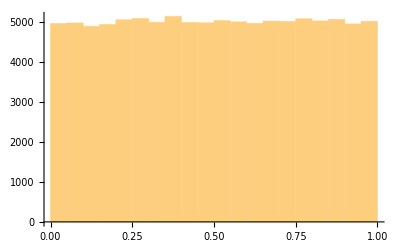

```mathematica
data=RandomVariate[NormalDistribution[],10^5];
data2 = Histogram[CDF[NormalDistribution[],data]]
```

### Experiment 2

```mathematica
GenNormal[n_]:= InverseCDF[NormalDistribution[],RandomVariate[UniformDistribution[],n]];
```

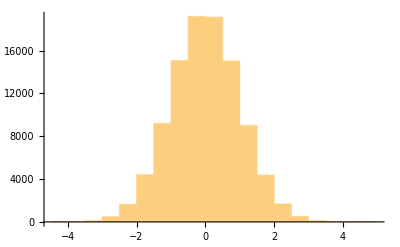

```mathematica
Histogram[GenNormal[10^5]]
```

## Arithmetic option

```mathematica
Residue[CDF[NormalDistribution[],1/x],{x,0}]
```

Residue[1/2 Erfc[-1/(√2 x)],{x,0}]